#### Code (Soon to be WFR)

```mathematica
HistogramBubbleChart[data : {{(_Real | _Integer), (_Real | _Integer)}...}, ops___]:=
BubbleChart[KeyValueMap[Append[#1, #2]&, Counts[data]], ops]
```

```mathematica
HistogramBubbleChart[data : {{{(_Real | _Integer), (_Real | _Integer)}...}...}, ops___]:=
BubbleChart[KeyValueMap[Append[#1, #2]&, Counts[#]]&/@ data, ops]
```

#### CAs

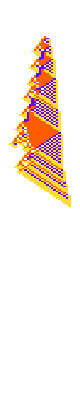
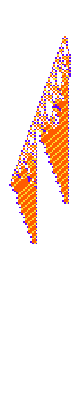
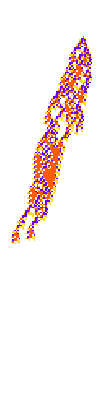
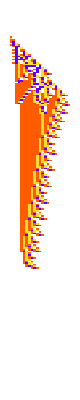
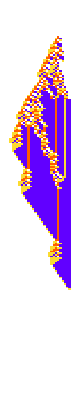
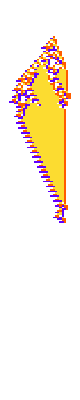
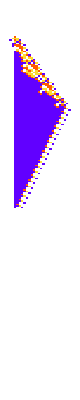
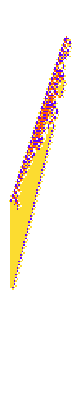

```mathematica
PlotCA/@{{329544069266708592463225775856558462236,4,1},{163313090342284595938913846502066693128,4,1},{31695255581700470911902716317105858104,4,1},{234969409870737885186155122705247389456,4,1},{305594030182245330593005536812098379020,4,1},{276033802575773574714948886195065539400,4,1},{100781445248190497550915302640180589452,4,1},{333412730384010924473712496196989406776,4,1},{43999191294040384362868476713575917896,4,1},{234876938465135365439119040628466918984,4,1},{280861221592569736193855132280195746312,4,1},{227135195378627184969662599411794102848,4,1}}
```

```mathematica
{{329544069266708592463225775856558462236,4,1},{163313090342284595938913846502066693128,4,1},{31695255581700470911902716317105858104,4,1},{234969409870737885186155122705247389456,4,1},{305594030182245330593005536812098379020,4,1},{276033802575773574714948886195065539400,4,1},{100781445248190497550915302640180589452,4,1},{333412730384010924473712496196989406776,4,1},{43999191294040384362868476713575917896,4,1},{234876938465135365439119040628466918984,4,1},{280861221592569736193855132280195746312,4,1},{227135195378627184969662599411794102848,4,1}}[[7]]
```

{100781445248190497550915302640180589452,4,1}

```mathematica
Table[PlotCA[PerturbedCellularAutomaton[{100781445248190497550915302640180589452,4,1}, {{1}, 0}, {110, {-50, 50}}]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PlotCA[PerturbedCellularAutomaton[{179079137400185473786391819702541282316,4,1}, {{1}, 0}, {200, {-50, 50}}]], 30]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PlotCA[PerturbedCellularAutomaton[{100781445248190497550915302640180589452,4,1}, {{1}, 0}, {200, {-50, 50}}]], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
```

```mathematica
ParallelTable[Module[{ru, ca, lt, pcas, fitness},
SeedRandom[7726778+i];
NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbCA[{ca, ru}, "Random"->1], Ceiling[lt/10]];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]
]//Last,{i,500}];
```

```mathematica
ParallelTable[Module[{ru, ca, lt, pcas, fitness},
SeedRandom[7726778+i];
NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbedCellularAutomaton[ru, {{1},0},{200, {-200, 200}}], Ceiling[lt/10]];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]
]//Last,{i,3}];
```

```mathematica
o =
```

{{{213009720930812998435984843612026570832,4,1},3},{{233962579560295818086524306191788971568,4,1},52},{{245281745961031408482530469677033861516,4,1},86}}

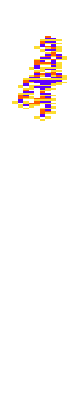
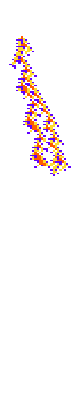
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotCA/@o[[All, 1]]
```

```mathematica
rob = ;
reg = ;
```

```mathematica
TestLifetime/@ rob[[All, 1]]
```

{23,5,118,83,118,74,144,43,28,4,106,10,28,21,97,71,5,119,6,81,98,84,95,105,81,120,11,91,6,100,5,88,10,99,16,2,4,58,99,139,91,91,26,90,1,98,83,2,4,21,89,102,82,69,175,58,44,81,88,64,114,137,106,11,3,68,1,163,85,108,100,92,4,66,30,9,13,71,43,24,107,49,92,52,1,155,5,76,72,78,50,35,22,88,100,88,96,102,111,72,93,103,86,98,114,16,17,96,10,112,13,83,3,5,80,113,16,94,5,130,95,131,61,5,86,95,31,81,1,3,18,190,88,20,133,10,87,103,10,42,60,79,55,70,55,8,5,127,1,12,72,55,14,97,58,95,49,17,34,48,1,11,4,90,74,10,74,78,38,82,183,50,110,13,124,61,173,6,121,42,1,77,7,6,1,76,77,88,5,70,94,1,80,19,10,21,4,65,72,97}

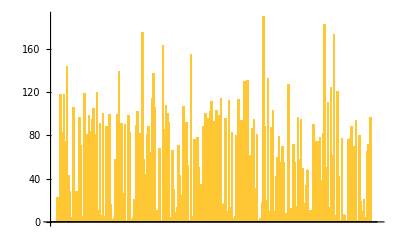

```mathematica
BarChart[]
```

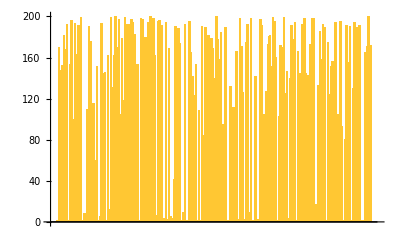

```mathematica
BarChart[TestLifetime/@ reg[[All, 1]]]
```

```mathematica
Max[]
```

190

```mathematica
PositionLargest[]
```

{132}

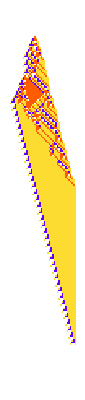

```mathematica
PlotCA@rob[[132, 1]]
```

```mathematica
Table[PlotCA[[rob[[132, 1]], {{1}, 0}, {200, {-200, 200}}, 1]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MapIndexed[Table[{First[#2], TestCALifeTime[[#, {{1}, 0}, {200, {-200, 200}}, 1]]}, 10]&, rob[[{132}, 1]]]
```

{{{1,189},{1,194},{1,101},{1,194},{1,194},{1,-∞},{1,194},{1,-∞},{1,137},{1,193}}}

```mathematica
SeedRandom[4444];
rps = MapIndexed[Prepend[Table[{First[#2], TestCALifeTime[[#, {{1}, 0}, {200, {-200, 200}}, 1]]}, 9], TestLifetime[#]]&, rob[[All, 1]]];
```

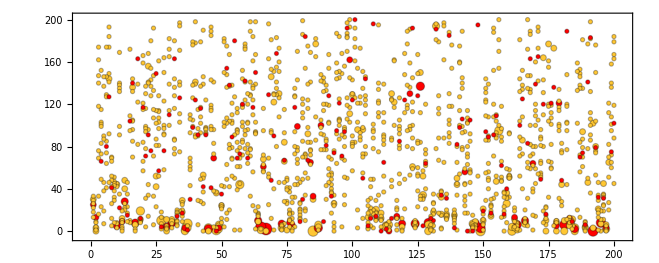

```mathematica
BubbleChart[Catenate[MapAt[Style[#, Red]&, #, 1]&/@
(KeyValueMap[Append[#1, #2]&, Counts[#]]&/@rps/.{x_, -Infinity}:> {x, 200})], PerformanceGoal->"Speed", AspectRatio->.4]
```

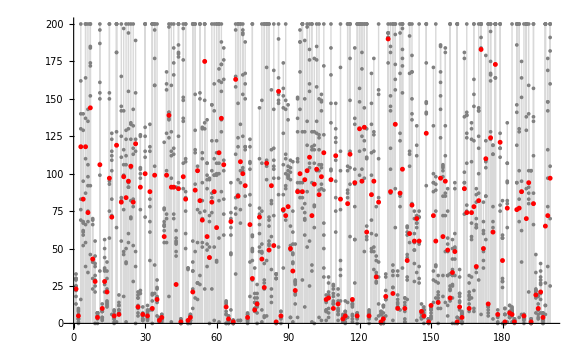

```mathematica
With[{pts =(rps/.{x_, -Infinity}:> {x, 200})},  Show[ListPlot[Catenate[pts], PlotStyle->Gray, Filling->Bottom, FillingStyle->LightGray], ListPlot[pts[[All, 1]], PlotStyle->{Red, PointSize[.006]}]]]
```

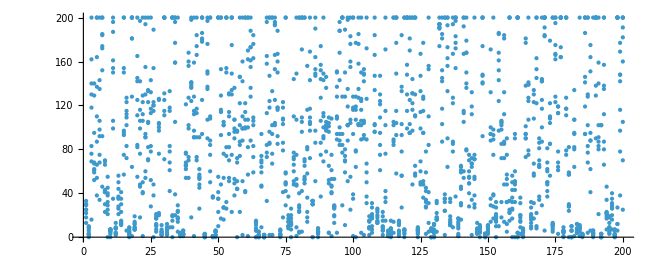

```mathematica
ListPlot[Catenate[MapAt[Style[#, Red]&, #, 1]&/@
(rps/.{x_, -Infinity}:> {x, 200})], PerformanceGoal->"Speed", AspectRatio->.4]
```

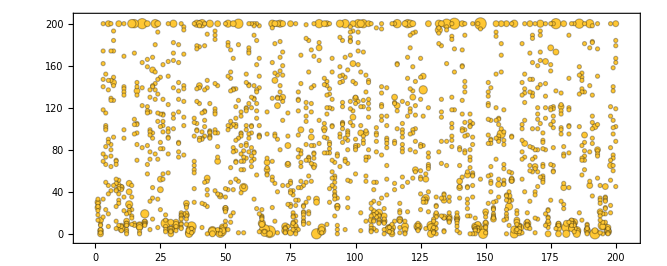

```mathematica
HistogramBubbleChart[Catenate[rps/.{x_, -Infinity}:> {x, 200}], PerformanceGoal->"Speed", AspectRatio->.4]
```

```mathematica
SeedRandom[4445];
alldists = 
ParallelMap[Function[rule, TestCALifeTime[[rule, {{1}, 0}, {250, {-50, 50}}, #]]&/@Prepend[Table[1,  29], <||>]], rob[[All, 1]]];
```

```mathematica
Iconize[alldists]
```

```mathematica
alldists = ;
```

```mathematica
adps = MapIndexed[Function[{val, idx}, {idx[[1]], #}&/@ val], alldists];
```

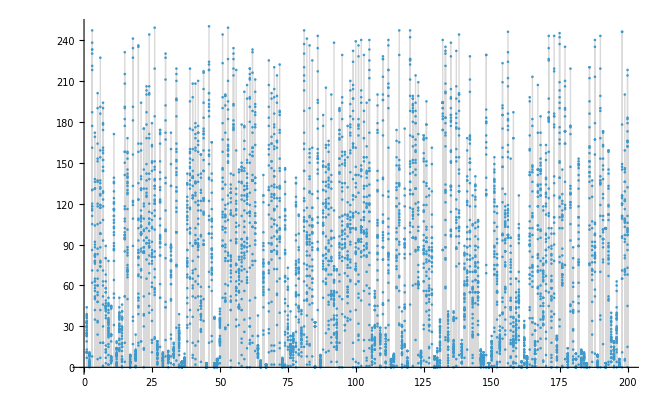

```mathematica
ListPlot[Catenate[adps], PlotHighlighting->None, Filling->Bottom, FillingStyle->LightGray]
```

```mathematica
Catenate[adps]/.{x_,-Infinity}:> {x, 250}
```

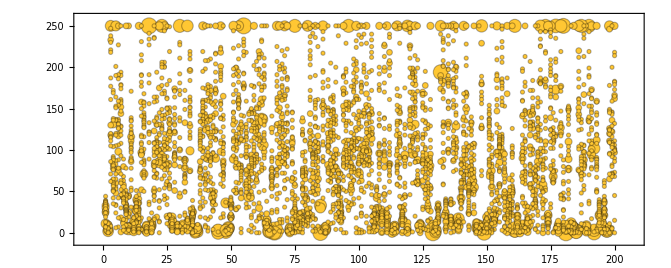

```mathematica
HistogramBubbleChart[Catenate[adps]/.{x_,-Infinity}:> {x, 250}, PerformanceGoal->"Speed", AspectRatio->.4]
```

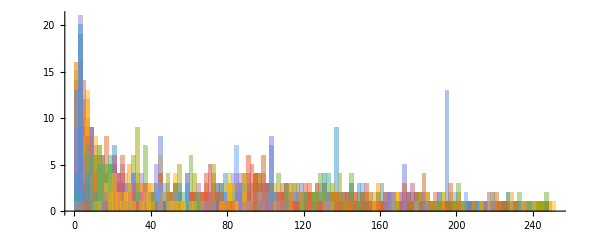

```mathematica
Histogram[alldists,{2}, PerformanceGoal->"Speed", AspectRatio->.4]
```

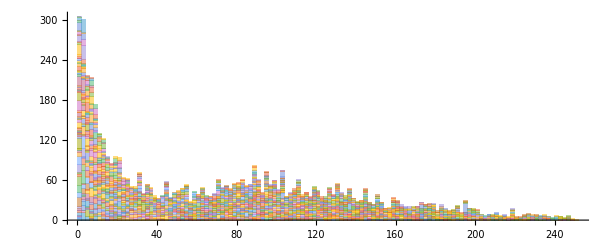

```mathematica
Histogram[alldists,{2}, PerformanceGoal->"Speed", AspectRatio->.4, ChartLayout->"Stacked"]
```

```mathematica
Histogram3D[Catenate[adps]/.{x_,-Infinity}:> {x, 250}, {{1}, Automatic}, PerformanceGoal->"Speed"]
```

-Graphics3D-

#### All plots

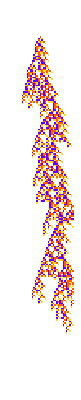
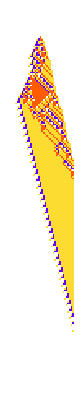
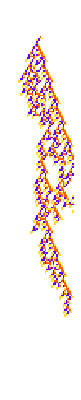
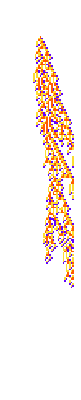
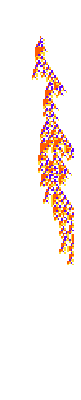
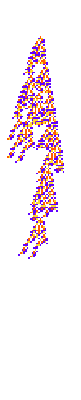
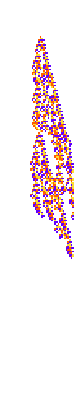
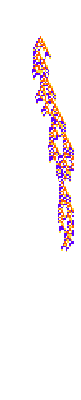

```mathematica
With[{cas = CellularAutomaton[#, {{1}, 0}, {200, {-20, 20}}]&/@ rob[[All, 1]]}, 
GraphicsGrid[Partition[
PlotCA[#,"Trim"->{None, None}, FrameStyle->LightGray]&/@ReverseSortBy[cas, TestCALifeTime],
32]]
]
```

```mathematica
With[{cas = CellularAutomaton[#, {{1}, 0}, {200, {-20, 20}}]&/@ reg[[All, 1]]}, 
GraphicsGrid[Partition[
PlotCA[#,"Trim"->{None, None}, FrameStyle->LightGray]&/@ReverseSortBy[cas, TestCALifeTime],
32]]
]
```

-Graphics-

```mathematica
With[{cas = CellularAutomaton[#, {{1}, 0}, {200, {-20, 20}}]&/@ reg[[All, 1]]}, PlotCA[#,"Trim"->{None, None}, FrameStyle->LightGray]&/@cas]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
reg[[101]]
```

{{332548750790689212550287704487994109824,4,1},140}

```mathematica
42, 44, 105
```

```mathematica
[[43]]
```

-Graphics-

```mathematica
[[181]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[PlotCA[CellularAutomaton[#, {{1}, 0}, {200, {-20, 20}}], "Trim"->{None, None}, ImageSize->50]&/@ rob[[All, 1]], 32], ImageSize->{650, Automatic}]
```

-Graphics-

```mathematica
ps = CAPolygon[CellularAutomaton[#, {{1}, 0}, {200, {-20, 20}}]]&/@ rob[[All, 1]];
```

```mathematica
ps[[130;;135]]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
ReverseSortBy[ps, Area][[;;10]]
```

{Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…],Polygon[…]}

```mathematica
GraphicsGrid[Partition[Graphics[#, PlotRange->{{0, 50}, {0, 200}}]&/@ ReverseSortBy[ps, Area][[10;;]], 32]]
```

-Graphics-

```mathematica
Graphics[Join[{Opacity[.025]}, ps[[120;;140]]], PlotRange->{{0, 50}, {0, 200}}]
```

-Graphics-

#### Finding evolution of our main regular

```mathematica
evo = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+101];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
];
```

```mathematica
evo = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+101];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
];
```

```mathematica
evo[[-1]]
```

{{252221615429535678116455102288646987792,4,1},1}

```mathematica
GraphicsRow[PlotCA[ArrayPad[#, 3]&/@CellularAutomaton[#, {{1}, 0}, 150],FrameStyle->Directive[Thin,Gray], "Trim"->{2, None}]&/@evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]], 1]], Spacings->10]
```

-Graphics-

```mathematica
PlotCA[evo[[-1, 1]]]
```

-Graphics-

#### Random vs. adapted

```mathematica
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[{FromDigits[#, 4], 4, 1}, {{1}, 0}, {200, {-200, 200}}], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {15 , 4^(2*1+1) - 1}]), 3], ImageSize->{600, Automatic}]
```

-Graphics-

```mathematica
SeedRandom[6666];
GraphicsGrid[Partition[ArrayPlot[CellularAutomaton[#,{{1}, 0}, {200, {-25, 25}}], ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]]& /@RandomSample[reg[[All, 1]], 16], 8]]
```

-Graphics-

#### Growth rates

```mathematica
CellularAutomaton[{FromDigits[#, 4], 4, 1}, {{1}, 0}, {200, {-200, 200}}]
```

```mathematica
pcas = With[{ru={299459058088077823758143088095350287424,4,1}},{{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-30, 40}}, #]&/@ {{"[◼]", "allperts"}}[CellularAutomaton[ru, {{1}, 0}, {400, {-30, 40}}]]];
```

```mathematica
widths=If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@#&/@pcas[[All,1]];
```

```mathematica
width0=If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {400, {-30, 40}}, <||>];
```

```mathematica
GraphicsRow[Show[ListStepPlot[Pick[widths,widths[[#,25]]<12&&widths[[#,25]]!=0&/@Range[Length[pcas]]],PlotRange->#,PlotStyle->RGBColor[0.95, 0.627, 0.1425],AspectRatio->.4,Frame->True,FrameLabel->{"time","width"}],ListStepPlot[width0,PlotStyle->RGBColor[0.24, 0.6, 0.8]]]&/@{{{0,50},{0,30}},{{0,240},Automatic}}]
```

```mathematica
SeedRandom[6666];
ListLinePlot[If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@CellularAutomaton[#,{{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 10], PlotRange->400, Filling->Bottom, PlotHighlighting->None, Frame->True, AspectRatio->.4, FrameLabel->{"steps", "width"}, PlotLabel->"Evolved"]
```

-Graphics-

```mathematica
SeedRandom[6666];
ListLinePlot[If[Length[#]===0,0,Last[#]-First[#]+1]&[{{"[◼]", "nonzeroRange"}}[#]]&/@CellularAutomaton[{FromDigits[#, 4], 4, 1},{{1}, 0}, 200]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {10 , 4^(2*1+1) - 1}]), PlotHighlighting->None,  Frame->True, AspectRatio->.4, FrameLabel->{"steps", "width"}, PlotLabel->"Random"]
```

-Graphics-

```mathematica
Length/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {15 , 4^(2*1+1) - 1}])
```

{64,64,64,64,64,64,64,64,64,64,64,64,64,64,64}

#### Rule frequency chart

```mathematica
{{"[◼]", "CustomStyleData"}}["Colors"]
```

{0→GrayLevel[1],1→Hue[0.06, 1, 1],2→Hue[0.73, 1, 1],3→Hue[0.14, 0.81, 0.99]}

```mathematica
BarChart[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)];
Flatten[BinCounts[digits, {0, 4, 1}]]]&/@ reg[[All, 1]], ChartLayout->"Overlapped", ChartStyle->(Opacity[.5, #]&)/@{{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]]]
```

-Graphics-

```mathematica
BarChart[
Transpose[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)];
Flatten[BinCounts[digits, {0, 4, 1}]]]&/@ reg[[All, 1]]], ChartLayout->"Overlapped", ChartStyle->(Opacity[.5, #]&)/@{{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]]]
```

-Graphics-

```mathematica
BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]], ChartLayout->"Stacked", ChartStyle->Lighter/@{{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]]]
```

-Graphics-

```mathematica
With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{10, 25}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*, Mesh->True, MeshStyle->Opacity[.4]*)]]& /@ RuleTuples[4, 1]}, BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]], ChartLayout->"Stacked", ChartBaseStyle->EdgeForm[Thickness[.1]], ChartStyle->((*Directive[*)Lighter[#](*, EdgeForm[Thickness[.1]]]*)&)/@{{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], ChartLabels->{aps, None}, LabelingSize->35, AspectRatio->.4, ImageSize->{600, Automatic}]]
```

-Graphics-

```mathematica
With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{10, 25}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*, Mesh->True, MeshStyle->Opacity[.4]*)]]& /@ RuleTuples[4, 1]}, BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]], ChartLayout->"Stacked", ChartBaseStyle->EdgeForm[Thickness[.1]], ChartStyle->(Directive[EdgeForm[Directive[Opacity[1], Gray]], Opacity[.8, #]]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], ChartLabels->{aps, None}, LabelingSize->35, AspectRatio->.4, ImageSize->{600, Automatic}]]
```

-Graphics-

```mathematica
Column[MapThread[Function[{digs,label}, With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{10, 25}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"](*, Mesh->True, MeshStyle->Opacity[.4]*)]]& /@ RuleTuples[4, 1]}, BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[digs], ChartLayout->"Stacked", ChartBaseStyle->EdgeForm[Thickness[.1]], ChartStyle->(Directive[EdgeForm[Directive[Opacity[1], Gray]], #]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], ChartLabels->{aps, None}, LabelingSize->35, AspectRatio->.4, ImageSize->{600, Automatic}, Frame->True, FrameLabel->{"rule", "counts"},PlotLabel->label]]],
{{(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {200 , 4^(2*1+1) - 1}]),Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]}, {"Random", "Evolved"}}]]
```

-Graphics-
-Graphics-

```mathematica
BarChart[Table[{1, 2 ,3 ,4}, 30], ChartLayout->"Stacked",ChartStyle->(Directive[#, EdgeForm[Black]]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]]]
```

-Graphics-

```mathematica
BarChart[Table[{1, 2, 3, 4}, 30], ChartLayout->"Stacked", ChartStyle->(Directive[EdgeForm[Directive[Opacity[1], Gray]], Lighter[#]]&)/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]]]
```

-Graphics-

```mathematica
Directive[EdgeForm[Directive[Opacity[1], Black]], Lighter[#]]&/@ {{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]]
```

```mathematica
xresall = ;
```

```mathematica
dat=
With[{ld ={{"[◼]", "Data"}}["$LifeData"]},  KeyValueMap[{x,y}|->{x,#}&/@y,{Count[#,True],Count[#,False]}&/@KeySort[Merge[{Map[Last,GroupBy[KeyValueMap[{ld[#1]["Year"],Union[#2]==={None}}&,xresall],First],{2}],Association[Table[y->{},{y,1969,2025}]]},Apply[Join]]]]];
```

```mathematica
BarChart[Reverse@{#[[1, 2]],Total[#[[All,2]]]}&/@dat, ChartStyle->{Directive[EdgeForm[Directive[Opacity[1], Darker[ColorData["DefaultPlotColors"][1]]]],Opacity[.6,ColorData["DefaultPlotColors"][1]]],Directive[EdgeForm[Directive[Opacity[1], Darker[Red]]], Lighter[Red]]}, ChartLayout->"Overlapped", 
Frame->True,PlotRange->All,AspectRatio->.4,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],FrameLabel->{None,"number of patterns"}, FrameTicks->{Automatic, {Table[{i, i + 1967},{i, 3, 57, 10}], Automatic}}]
```

```mathematica
Histogram[Values[#Year&/@{{"[◼]", "Data"}}["$LifeData"]],{1},Frame->True,TicksStyle->GrayLevel[.25] ,FrameTicksStyle->GrayLevel[.25],AspectRatio->.4,FrameLabel->{"year",None},GridLines->{Range[1970,2020,10],None}, ChartStyle->Directive[Opacity[.6,ColorData["DefaultPlotColors"][1]],EdgeForm[Darker[ColorData["DefaultPlotColors"][1]]]]]
```

```mathematica
With[{aps = Rasterize[ArrayPlot[List/@#,ImageSize->{20, 30}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]]& /@ RuleTuples[4, 1]}, BarChart[BinCounts[#, {0, 4, 1}]&/@Transpose[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ reg[[All, 1]]], ChartLayout->"Stacked", ChartStyle->Lighter/@{{"[◼]", "CustomStyleData"}}["Colors"][[All, 2]], LabelingFunction->(Placed[aps[[#2[[1]]]], Below]&)]]
```

-Graphics-

```mathematica
BarChart[{1, 2, 3}]
```

```mathematica
Module[{n, k, r}, 
{n, k, r} =interpretrule[#];
RuleTuples[k, r]
```

```mathematica
RuleTuples[4, 1]
```

{{3,3,3},{3,3,2},{3,3,1},{3,3,0},{3,2,3},{3,2,2},{3,2,1},{3,2,0},{3,1,3},{3,1,2},{3,1,1},{3,1,0},{3,0,3},{3,0,2},{3,0,1},{3,0,0},{2,3,3},{2,3,2},{2,3,1},{2,3,0},{2,2,3},{2,2,2},{2,2,1},{2,2,0},{2,1,3},{2,1,2},{2,1,1},{2,1,0},{2,0,3},{2,0,2},{2,0,1},{2,0,0},{1,3,3},{1,3,2},{1,3,1},{1,3,0},{1,2,3},{1,2,2},{1,2,1},{1,2,0},{1,1,3},{1,1,2},{1,1,1},{1,1,0},{1,0,3},{1,0,2},{1,0,1},{1,0,0},{0,3,3},{0,3,2},{0,3,1},{0,3,0},{0,2,3},{0,2,2},{0,2,1},{0,2,0},{0,1,3},{0,1,2},{0,1,1},{0,1,0},{0,0,3},{0,0,2},{0,0,1},{0,0,0}}

```mathematica
lf = 
With[{aps = ArrayPlot[List[#],ImageSize->{20, 30}]& /@ RuleTuples[4, 1]}, Placed[aps[[#2[[2]]]],Below]]&
```

$Aborted

```mathematica
ArrayPlot[List/@#,ImageSize->{20, 30}, ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]& /@ RuleTuples[4, 1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### highlighting edge rules

```mathematica
bodyidxs[]
```

```mathematica
edgerules = Most[RuleTuples[4, 1][[{16, 32, 48, 61, 62, 63, 64}]]]
```

{{3,0,0},{2,0,0},{1,0,0},{0,0,3},{0,0,2},{0,0,1}}

```mathematica
Range[{{1, }}]
```

```mathematica
SeedRandom[6666];
Function[ca, 
Module[{b = Array[0 &, {Length[ca], Length[ca[[1]]]}]}, 
gray = ReplacePart[b, Thread[bodyidxs[ca]-> 1]];
redidxs = 
MapIndexed[
Function[{row, idx},( ({#, idx[[1]]}&)/@Range[First[SequencePosition[row, #]]]&)/@ edgerules], ca]]]/@ (CellularAutomaton[#, {{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 1])
```

First::nofirst: {} has zero length and no first element.

Range::range: Range specification in Range[First[{}]] does not have appropriate bounds.

First::nofirst: {} has zero length and no first element.

Range::range: Range specification in Range[First[{}]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
Range@@@{{2, 4}}
```

{{2,3,4}}

```mathematica
SeedRandom[6666];

Function[rules, Function[ca, 
Module[{b = Array[0 &, {Length[ca], Length[ca[[1]]]}]}, 
gray = ReplacePart[b, Thread[bodyidxs[ca]-> 1]];
redidxs = 
MapIndexed[Function[{val, idx}, {idx[[1]], #}&/@ val], DeleteCases[(Flatten/@Function[row, If[# === {}, {}, Range@@@#]&[SequencePosition[row, #]]&/@ edgerules]/@ca), {}]];
ArrayPlot[ReplacePart[gray, Thread[redidxs->2]], ColorRules->{0->White, 1->LightGray, 2->Red}]
]]/@ (CellularAutomaton[#, {{1}, 0}, 200]&/@RandomSample[rules, 10])]/@ {reg[[All, 1]], {FromDigits[#, 4], 4, 1}&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {10 , 4^(2*1+1) - 1}])}
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
SeedRandom[6666];

GraphicsRow[Function[ca, 
Module[{b = Array[0 &, {Length[ca], Length[ca[[1]]]}]}, 
gray = ReplacePart[b, Thread[bodyidxs[ca]-> 1]];
redidxs = 
MapIndexed[Function[{val, idx}, {idx[[1]], #}&/@ val], DeleteCases[(Flatten/@Function[row, If[# === {}, {}, Range@@@#]&[SequencePosition[row, #]]&/@ edgerules]/@ca), {}]];
ArrayPlot[ReplacePart[gray, Thread[redidxs->2]], ColorRules->{0->White, 1->LightGray, 2->Red}]
]]/@ (CellularAutomaton[#, {{1}, 0}, 200]&/@RandomSample[reg[[All, 1]], 10])]
```

-Graphics-

```mathematica
Map[Length, ]
```

{201}

```mathematica
SequencePosition[{{1, 2, 3}, {4, 5, 6}}, {1, 2}]
```

{}

```mathematica
SeedRandom[6666];
PlotCA/@RandomSample[reg[[All, 1]], 1]
```

{-Graphics-}

#### Using big yellow as an example of results under perturbation

```mathematica
132
```

```mathematica
SeedRandom[426778+132];
NestList[CompoundExpression[
ru=randomrulemutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbCAFast[{ca, ru}, "Random"->1, lt],5];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
SeedRandom[426778+132];
perts = Reap[bye = NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = TestCALifeTime[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[PerturbedCellularAutomaton[ru,{{1}, 0},{200, {-200, 200}}],5];
Sow[{ru, pcas[[All, 2]]}];
fitness = Min[Join[{lt}, TestCALifeTime/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]][[2, 1]];
```

```mathematica
PlotCA/@bye[[ResourceFunction["ProgressiveMaxPositions"][bye[[All, -1]]], 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Position[bye[[All, 1]],{297413941736398172128300269684090721592,4,1}]
```

{}

```mathematica
Length[perts]
```

1196

```mathematica
kept = Select[perts, MemberQ[bye[[All, 1]],#[[1]]]&] ;
```

```mathematica
Length[kept]
```

129

```mathematica
kept[[75]]
```

{{68493217158078976165312430091434196280,4,1},{<|{7,198}→1|>,<|{8,198}→2|>,<|{7,200}→0|>,<|{8,197}→0|>,<|{6,200}→2|>}}

```mathematica
PlotCA[perts[[750, 1]]]
```

-Graphics-

```mathematica
Length[kept]
```

129

```mathematica
Function[{ru, perts}, PlotCA[PerturbedCellularAutomaton[ru, {{1}, 0}, {90,  {-200, 200}}, #]]&/@ perts]@@kept[[105]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ResourceFunction["ProgressiveMaxPositions"][bye[[All, -1]]]
```

{1,10,154,243,268,412,506,637,782,790,802,893,907,942,1140,1578}

```mathematica
bye[[ResourceFunction["ProgressiveMaxPositions"][bye[[All, -1]]], 1]][[9]]
```

{297413941736399379873447198801621939512,4,1}

```mathematica
SeedRandom[426778+132];
GraphicsRow[Table[PlotCA[PerturbedCellularAutomaton[bye[[ResourceFunction["ProgressiveMaxPositions"][bye[[All, -1]]], 1]][[9]],{{1}, 0}, {200, {-200, 200}}]], 5]]
```

-Graphics-

#### Distribution charts

```mathematica
samplts = ParallelMap[Table[TestCALifeTime[{{"[◼]", "PerturbedCellularAutomaton"}}[#,{{1},0},{200,{-100,100}}]], 200]&,rob[[sortedidxs[[;;10]], 1]]];
```

```mathematica
Histogram[( samplts/.-Infinity->0)[[1]]]
```

-Graphics-

```mathematica
Histogram/@( samplts/.-Infinity->0)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
BarChart[N/@Mean/@(samplts/.-Infinity->0)]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Histogram[#, {5}]&/@(samplts/.-Infinity->0), 5]]
```

-Graphics-

```mathematica
Histogram[(samplts/.-Infinity->0),{5}, ChartLayout->{"Row", 2}, FrameStyle->Directive[Thickness[.001], Lighter[Gray]]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[MapIndexed[BarChart[#,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  Table[{i, 10i}, {i, 0,20, 5}], None], Automatic}}, BarSpacing->None, ImageSize->{If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  205, 215], Automatic}]&, MapAt[Style[#, (*Lighter[Red, .3]*)Red]&, BinCounts[#, {10}]&/@(samplts[[;;6]]/.-Infinity->210), {All, -1}]], 3], Spacings->0]
```

-Graphics-

```mathematica
Histogram[(samplts[[;;6]]/.-Infinity->205),{5}, ChartLayout->{"Row", 3}, ImageSize->{650, Automatic}]
```

-Graphics-

```mathematica
Select[rob, TestCALifeTime[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&]
```

{{{148929425018041907435018990866096194332,4,1},103},{{172092766817343873409073563946540618248,4,1},87},{{10489820457880410334416158284057339664,4,1},135},{{188517040261626961100942985584095523132,4,1},89},{{300061868905989881377334129300752641168,4,1},113},{{106791988555589660962904136479185707072,4,1},105},{{277890604414540793017520420061793457800,4,1},114},{{82824521677923888872225559982496556864,4,1},124},{{25188170208739390129512598335163286300,4,1},102},{{91922824165792219657077459405861558016,4,1},129},{{300994971936240100546501727127483511560,4,1},107},{{104181663558246934410580700637598330184,4,1},123},{{266043814425295209094236938680998211384,4,1},106},{{297740496109707853422502582639865659960,4,1},121},{{239439090661623187740448743369010004028,4,1},108},{{23422150084464011682677532665552835912,4,1},107},{{219407992627004466489656322368192385292,4,1},154},{{237523611031539016077526641623662087944,4,1},102},{{220628780842782624481246402253509403528,4,1},111},{{59489898285211696587237550624014501128,4,1},103},{{53163811228344453032742105794023376700,4,1},114},{{208691650261327780766642805129944240952,4,1},103},{{108011836692393053903646382465252469532,4,1},102},{{16656018739946216765992316861998438668,4,1},112},{{221897589461974070374975172689655766664,4,1},112},{{297413941736400589979939780692294751544,4,1},190},{{259501172722806427164596581925170679048,4,1},99},{{113052830365670227486229876074066578572,4,1},103},{{327641399188816567262038562908943131656,4,1},100},{{67143636050057692643906547803754269448,4,1},127},{{287466238189489910834374673537453787532,4,1},105},{{18098836799129975907561517670825114496,4,1},124},{{134128438940045403733091768047090105144,4,1},145},{{98774160147102787331059415600640003984,4,1},121}}

```mathematica
Select[reg, TestCALifeTime[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&]
```

```mathematica
Length[]
```

34

```mathematica
ReverseSortBy[samplts/.-Infinity->0, Mean]
```

{{182,182,178,0,0,194,170,0,0,0,182,194,0,74,162,0,194,195,194,194,174,194,162,194,194,200,194,194,194,166,194,0,0,198,191,0,190,194,194,0,197,190,194,196,0,194,198,194,186,194,170,0,0,0,194,0,190,194,192,158,190,194,194,190,0,194,194,0,0,194,0,194,169,154,194,194,178,194,0,190,170,194,198,194,0,198,194,0,194,189,194,194,0,198,194,194,194,181,190,190,0,0,0,0,194,198,170,186,80,0,194,0,186,0,0,0,194,170,190,147,190,182,0,93,158,197,194,137,103,0,182,194,0,0,194,0,191,174,190,0,194,190,0,131,0,186,1,0,0,0,166,194,0,174,0,190,114,194,181,194,0,190,178,47,166,194,0,0,0,194,190,186,0,178,0,0,194,0,194,194,0,198,194,194,186,182,0,194,194,190,190,198,194,198,194,190,194,194,0,90},{109,117,181,6,137,0,89,107,24,137,163,68,18,28,116,0,191,78,98,136,85,155,137,137,0,146,100,142,60,137,161,189,112,142,137,90,182,137,0,122,133,0,0,137,123,137,0,74,1,112,137,142,148,23,137,83,0,74,146,128,145,95,134,135,121,137,0,119,104,137,42,130,120,0,100,132,141,23,45,0,81,160,121,137,142,0,153,0,97,94,184,137,105,137,137,137,55,137,147,130,97,137,137,137,116,163,101,189,132,136,0,164,25,130,108,92,133,52,146,18,84,137,81,46,138,145,98,136,140,128,119,87,182,173,135,142,137,137,117,200,102,122,131,22,35,101,142,136,171,166,95,107,138,72,137,22,200,139,75,112,182,111,113,0,62,121,200,161,140,104,137,137,102,61,120,137,197,137,67,172,0,120,84,166,68,91,190,116,0,169,69,156,137,156,144,158,96,135,190,122},{150,23,124,128,38,163,139,66,187,139,0,74,144,0,138,142,90,104,139,138,106,50,71,23,46,114,0,134,150,24,137,0,124,124,0,198,60,148,139,0,0,143,124,0,120,0,124,139,27,141,137,152,104,139,139,0,156,72,107,198,177,30,124,155,77,187,107,139,128,141,48,139,141,149,200,23,137,167,198,0,124,40,53,28,46,152,152,139,124,65,89,124,105,152,151,104,0,112,145,152,0,144,128,163,124,0,0,126,198,139,171,124,198,139,148,0,60,55,124,98,70,0,153,33,139,138,90,136,139,128,81,152,124,0,198,138,198,139,0,124,198,139,159,139,198,92,33,198,90,56,0,148,150,126,98,124,198,187,90,141,167,139,139,35,0,154,144,198,149,161,114,198,146,140,63,140,97,60,27,139,128,79,124,198,198,0,139,94,187,0,168,18,139,141,145,100,124,69,60,124},{0,0,0,0,42,197,144,1,155,155,155,0,0,72,196,155,196,0,0,134,155,110,86,0,104,82,53,180,98,161,83,192,153,197,87,11,87,97,110,69,183,150,155,169,169,105,87,121,185,119,155,115,157,66,0,183,111,124,181,150,153,107,0,167,0,155,162,91,109,0,110,100,65,155,22,86,40,59,155,60,187,140,155,157,155,155,54,63,0,0,0,0,96,20,180,86,80,37,155,63,155,117,0,81,147,159,175,153,73,182,108,148,183,155,81,155,0,155,100,83,172,116,58,120,152,25,155,171,51,117,0,154,111,136,107,14,101,0,158,159,155,0,103,0,153,157,164,155,0,190,0,158,153,170,144,175,131,24,53,92,185,155,0,7,155,94,0,103,190,0,37,155,86,144,103,140,109,168,140,86,199,161,0,152,168,175,155,103,0,155,86,50,0,155,81,168,140,97,130,93},{101,92,91,121,0,151,117,69,98,126,156,111,116,0,138,150,92,49,0,0,58,87,58,194,150,110,0,94,122,0,91,120,49,167,92,0,0,145,75,30,29,103,161,124,0,0,30,97,109,113,91,0,186,0,0,137,0,133,147,135,0,0,0,0,99,128,0,91,195,114,163,0,29,100,150,182,88,194,200,0,0,61,57,88,117,190,140,145,96,135,0,90,0,93,132,0,55,109,124,0,175,0,100,104,32,163,0,160,119,95,133,158,132,199,95,102,93,87,114,51,112,0,90,104,12,120,165,145,138,133,132,135,0,34,160,0,110,67,120,57,128,177,29,0,132,137,64,93,91,122,133,143,100,56,141,197,135,190,0,177,104,61,152,133,88,70,133,150,150,121,183,156,0,133,152,0,133,132,0,163,133,133,161,104,46,0,0,170,138,104,0,133,0,0,151,173,0,98,169,0},{0,153,166,163,0,177,0,96,21,71,171,163,123,132,178,0,114,167,162,128,14,105,172,0,0,0,153,0,160,134,67,0,166,129,186,104,91,161,59,161,138,21,155,187,166,71,0,38,0,173,184,41,174,168,0,36,170,0,9,34,172,76,109,184,71,83,109,122,79,138,42,29,153,48,124,177,10,0,0,163,34,142,158,0,0,91,184,6,30,171,156,119,15,66,65,0,117,114,119,163,147,95,0,177,165,0,107,0,163,107,1,135,29,0,100,129,0,170,17,163,109,199,115,0,177,92,168,164,0,114,130,110,120,168,106,163,0,166,4,4,105,159,0,102,162,191,45,194,168,0,53,0,0,0,39,0,130,42,0,130,104,48,102,188,0,76,4,0,21,155,135,47,14,155,22,98,196,161,116,91,0,86,134,144,68,0,110,144,0,116,129,135,80,109,57,85,81,0,46,102},{0,190,0,0,145,199,0,0,0,119,0,0,170,173,119,185,164,173,173,169,93,0,173,0,0,173,164,0,0,166,0,0,0,0,28,180,0,0,173,0,158,1,164,158,0,0,6,0,173,17,186,184,179,0,0,176,139,0,64,0,106,0,199,197,0,0,67,0,0,199,173,0,136,164,158,106,0,0,173,93,173,145,168,0,138,80,0,0,0,0,157,0,186,109,0,116,147,173,150,0,130,0,153,145,0,150,0,173,171,0,0,0,173,173,0,0,0,0,0,0,0,76,189,3,175,80,0,0,0,158,0,199,190,0,171,173,173,0,0,173,0,173,173,173,95,0,0,0,173,158,175,183,89,0,187,181,180,171,0,117,185,172,105,0,182,0,0,181,0,173,190,41,0,0,171,182,164,0,160,0,126,0,0,149,119,176,183,164,0,0,0,183,173,145,0,0,173,0,0,0},{144,70,29,0,0,103,104,101,150,114,0,134,54,90,144,141,105,126,110,185,175,132,51,152,138,136,150,160,33,144,144,31,35,131,0,132,104,30,84,185,0,96,118,0,67,144,0,28,164,152,144,110,78,98,0,0,108,50,0,0,94,163,146,144,148,160,48,117,154,69,3,59,114,117,24,185,29,123,108,60,151,18,117,44,0,79,43,143,147,149,97,38,56,191,0,0,108,54,169,0,155,144,8,70,0,37,126,85,91,183,150,144,49,16,0,173,60,156,0,0,43,128,0,69,0,158,170,183,0,109,43,103,79,133,91,59,0,0,0,0,0,10,144,171,142,107,0,152,0,0,0,0,144,71,174,31,46,156,0,70,142,146,0,0,118,54,29,0,123,157,144,130,75,0,0,142,63,0,141,144,0,160,25,103,144,31,0,144,0,125,145,144,0,144,0,57,144,0,155,173},{158,0,0,0,0,0,0,0,129,0,0,0,115,183,183,151,0,0,0,73,22,0,48,0,182,175,0,0,0,0,83,0,103,179,123,0,123,51,108,165,183,0,89,0,0,138,172,140,0,181,0,0,183,22,62,0,101,0,0,71,135,0,183,168,159,0,68,171,0,0,183,0,83,0,183,183,0,183,162,0,148,183,0,0,0,191,0,0,183,174,0,158,140,192,83,0,0,0,183,0,44,86,0,111,183,0,78,0,0,0,112,151,117,0,199,0,0,0,0,0,170,0,0,0,0,0,0,0,0,194,147,173,87,0,0,0,117,183,0,62,123,183,114,102,0,0,51,183,199,79,122,171,69,183,47,80,185,171,175,9,0,152,0,0,0,0,0,102,0,0,63,0,0,0,190,109,183,0,185,183,178,130,0,69,0,0,0,0,182,183,193,159,153,165,136,200,181,0,0,0},{111,0,72,0,132,175,0,0,74,26,0,0,39,0,182,0,178,179,179,40,0,171,0,189,0,99,111,37,0,0,130,0,175,129,0,76,0,132,176,22,0,0,129,78,0,0,176,114,0,129,169,191,1,0,116,175,0,169,0,169,0,173,0,142,0,74,122,135,0,0,0,0,0,173,0,179,191,50,176,131,84,125,199,123,98,0,177,137,0,133,197,64,175,0,179,11,195,0,67,12,52,0,0,0,0,163,0,23,175,50,198,0,0,0,65,0,175,40,177,175,0,154,0,141,0,0,0,72,0,0,0,41,115,0,0,0,0,0,128,179,0,0,132,0,100,22,178,138,0,0,123,103,0,0,0,46,175,0,0,11,175,0,178,107,0,90,175,35,175,175,133,0,0,175,0,0,182,175,0,0,176,0,0,0,0,176,143,170,187,132,0,0,175,115,0,0,0,189,0,0}}

#### Better overall plot

```mathematica
PlotCA[CellularAutomaton[#, {{1}, 0}, 200]]&/@ rob[[sortedidxs[[;;10]], 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Mod[12, 5]
```

2

```mathematica
ListPlot[MapIndexed[
Module[{ca = CellularAutomaton[#, {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
If[Mod[#2[[1]], 20] == 1, Callout[lt, PlotCA[ArrayPad[#, 1]&/@ca,"Trim"->{None, 5}, ImageSize->{Automatic,25 Sqrt[1+lt]}], LabelVisibility->All], TestCALifeTime[ca]]]&, rob[[sortedidxs, 1]]], LabelingSize->50, Filling->Bottom]
```

-Graphics-

```mathematica
SeedRandom[5558];
r = RandomSample[Range[Length[rob]], 10];
```

```mathematica
ListPlot[MapIndexed[
Module[{ca = CellularAutomaton[#, {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
If[MemberQ[r, #2[[1]]],Callout[lt, PlotCA[ArrayPad[#, 1]&/@ca,"Trim"->{None, 5}, ImageSize->{Automatic,25 Sqrt[1+lt]}], LabelVisibility->All], TestCALifeTime[ca]]]&, rob[[sortedidxs, 1]]], LabelingSize->50, Filling->Bottom, AspectRatio->.4]
```

-Graphics-

```mathematica
ListPlot[MapIndexed[
Module[{ca = CellularAutomaton[#, {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
If[MemberQ[r, #2[[1]]],Callout[lt, PlotCA[ArrayPad[#, 1]&/@ca,"Trim"->{None, 5}, ImageSize->{Automatic,25 Sqrt[1+lt]}], LabelVisibility->All], TestCALifeTime[ca]]]&, reg[[sireg, 1]]], LabelingSize->50, Filling->Bottom, AspectRatio->.4]
```

-Graphics-

```mathematica
Column[MapThread[Function[{idxs, labs}, 
ListPlot[MapIndexed[
Module[{ca = CellularAutomaton[#, {{1}, 0}, 200], lt},
lt = TestCALifeTime[ca];
If[MemberQ[r, #2[[1]]],Callout[lt, PlotCA[ArrayPad[#, 1]&/@ca,"Trim"->{None, 5}, ImageSize->{Automatic,25 Sqrt[1+lt]}], LabelVisibility->All], TestCALifeTime[ca]]]&, idxs], LabelingSize->50, Filling->Bottom, AspectRatio->.4, ImageSize->{400, Automatic}, PlotRange->{{0, 200}, {0, 250}}, PlotLabel->labs, Frame->True, FrameLabel->{"pattern", "lifetime"}]], {{reg[[sireg, 1]], rob[[sortedidxs, 1]]}, {"Regular Evolution", "Perturbed Evolution"}}]]
```

-Graphics-
-Graphics-

```mathematica
BarChart[With[{ca = CellularAutomaton[#, {{1}, 0}, 200]},Callout[TestCALifeTime[ca],PlotCA[ca]]]&/@ rob[[sortedidxs, 1]]]
```

-Graphics-

#### dc v2

```mathematica
Select[rob, ]
```

```mathematica
samplts = ParallelMap[Table[TestCALifeTime[{{"[◼]", "PerturbedCellularAutomaton"}}[#,{{1},0},{200,{-100,100}}]], 200]&,rob[[sortedidxs[[;;10]], 1]]];
```

$Aborted

```mathematica
GraphicsGrid[Partition[MapIndexed[BarChart[#,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  Table[{i, 10i}, {i, 0,20, 5}], None], Automatic}}, BarSpacing->None, ImageSize->{If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  205, 215], Automatic}]&, MapAt[Style[#, (*Lighter[Red, .3]*)Red]&, BinCounts[#, {10}]&/@(samplts[[;;6]]/.-Infinity->210), {All, -1}]], 3], Spacings->0]
```

```mathematica
l1 = Select[rob, TestCALifeTime[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&];
```

```mathematica
samplts = ParallelMap[Table[TestCALifeTime[{{"[◼]", "PerturbedCellularAutomaton"}}[#,{{1},0},{200,{-100,100}}]], 200]&,l1[[All, 1]]];
```

```mathematica
zd = (samplts /. -Infinity->0);
```

```mathematica
bmi = With[{zd = (samplts /. -Infinity->0)}, 
ReverseSortBy[Range[Length[l1]],Mean[zd[[#]]]&]];
```

```mathematica
means = N[Mean/@ zd];
```

```mathematica
MapIndexed[BarChart[ReplacePart[#,10->Callout[#[[10]], PlotCA[l1[[bmi[[#2[[1]]]], 1]], "Trim"->{1, 3}], Above, Appearance->None]] ,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  Table[{i, 5i}, {i, 0,50, 10}], None], Automatic}}, BarSpacing->None, ImageSize->{If[#2[[1]] == 4 || #2[[1]] == 5 ||#2[[1]] == 6,  205, 215], Automatic}, (*ChartLabels->{Placed[PlotCA[l1[[bmi[[#2[[1]]]], 1]], "Trim"->{1, 3}], Above]}, *)LabelingSize->85, PlotRange->150, PlotRangePadding->{Automatic, 0}]&, 
MapAt[Style[#, (*Lighter[Red, .3]*)Red]&, BinCounts[#, {5}]&/@(samplts[[bmi[[;;6]]]]/.-Infinity->210), {All, -1}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grid[Partition[MapIndexed[BarChart[ReplacePart[#,10->Callout[#[[10]], PlotCA[l1[[bmi[[#2[[1]]]], 1]], "Trim"->{1, 3}], Above, Appearance->None]] ,PlotRange->100,Frame->True, FrameTicks->{{If[#2[[1]] == 1 || #2[[1]] == 4, Automatic, None],Automatic}, {If[4 <=#2[[1]] <= 6,  Table[{i, 5i}, {i, 0,50, 10}], None], Automatic}}, BarSpacing->None,ImageSize->{If[#2[[1]] == 1 || #2[[1]] == 4,245, 225], Automatic} , LabelingSize->85, PlotRange->150, PlotRangePadding->{Automatic, 0},
Epilog->{Dotted, Red, Line[{{means[[bmi[[#2[[1]]]]]]/5, 100}, {means[[bmi[[#2[[1]]]]]]/5, 0}}]}
]&, 
MapAt[Style[#,Red]&, BinCounts[#, {5}]&/@(samplts[[bmi[[;;6]]]]/.-Infinity->210), {All, -1}]], 3]]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
ImageSize->{If[#2[[1]] == 1 ,  225,If[#2[[1]] == 4, 225,  205]], Automatic}
```

```mathematica
ltdistchart[]
```

```mathematica
(samplts /. -Infinity->0)
```

```mathematica
Histogram/@ (samplts /. -Infinity->0)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Causal rule graph

```mathematica
getsubs[l1[[bmi[[1]], 1]]]
```

{{3,3,3}→3,{3,3,2}→1,{3,3,1}→3,{3,3,0}→3,{3,2,3}→2,{3,2,2}→3,{3,2,1}→3,{3,2,0}→3,{3,1,3}→3,{3,1,2}→1,{3,1,1}→1,{3,1,0}→3,{3,0,3}→1,{3,0,2}→3,{3,0,1}→1,{3,0,0}→0,{2,3,3}→3,{2,3,2}→1,{2,3,1}→2,{2,3,0}→3,{2,2,3}→0,{2,2,2}→3,{2,2,1}→3,{2,2,0}→2,{2,1,3}→1,{2,1,2}→1,{2,1,1}→0,{2,1,0}→2,{2,0,3}→3,{2,0,2}→0,{2,0,1}→2,{2,0,0}→0,{1,3,3}→1,{1,3,2}→1,{1,3,1}→2,{1,3,0}→1,{1,2,3}→1,{1,2,2}→3,{1,2,1}→1,{1,2,0}→1,{1,1,3}→0,{1,1,2}→1,{1,1,1}→1,{1,1,0}→3,{1,0,3}→3,{1,0,2}→3,{1,0,1}→3,{1,0,0}→3,{0,3,3}→2,{0,3,2}→2,{0,3,1}→1,{0,3,0}→0,{0,2,3}→2,{0,2,2}→0,{0,2,1}→2,{0,2,0}→3,{0,1,3}→3,{0,1,2}→1,{0,1,1}→1,{0,1,0}→1,{0,0,3}→0,{0,0,2}→3,{0,0,1}→2,{0,0,0}→0}

```mathematica
PerturbationSensitivityGraphs[{CellularAutomaton[l1[[bmi[[1]], 1]],{{1}, 0}, 200],l1[[bmi[[1]], 1]]}]
```

Part::take: Cannot take positions 0 through 29 in {0,3,2,3,3,1,1,1,0,1,3,0,1,1,1,1,1,0,1,3,3,1,1,3,0,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0}.

Part::take: Cannot take positions 0 through 29 in {0,2,2,3,3,1,1,3,3,3,1,1,1,1,1,1,3,3,3,1,3,1,0,1,1,2,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0}.

Part::take: Cannot take positions -1 through 29 in {3,0,0,3,3,1,0,1,3,3,1,1,1,1,1,0,1,3,3,3,2,3,3,1,1,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0}.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 2 in Complement[{0,1,2,3},Part].

Part::partw: Part 1 of Part[] does not exist.

Part::partw: Part 2 of Part[] does not exist.

Part::partw: Part 1 of Complement[{0,1,2,3},Part][] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Complement::normal: Nonatomic expression expected at position 2 in Complement[{0,1,2,3},Part].

$Aborted[]

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Style[#1,#2]&].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[Missing[KeyAbsent,Style[#1,#2]&]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

$Aborted[]

WeaklyConnectedGraphComponents::graph: A graph object is expected at position 1 in WeaklyConnectedGraphComponents[GraphPlot[«1»]].

General::stop: Further output of WeaklyConnectedGraphComponents::graph will be suppressed during this calculation.

```mathematica
NestGraph[]
```

```mathematica
PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {{2}, 3},{5, {-2, 2}}]]
```

-Graphics-

```mathematica
PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {{2}, 3},{5, {-2, 2}}]]
```

```mathematica
ResourceFunction["SubstitutionSystemCausalGraph"][getsubs[l1[[bmi[[1]], 1]]],{3, 2, 3},2]
```

-Graphics-

```mathematica
SubstitutionSystem[{0->{0,1},1->{0}},{0},5]
```

```mathematica
ResourceFunction["SubstitutionSystemCausalGraph"][{{0, 1}->{1, 0, 0, 0, 1}},{0, 1},2]
```

[{{0,1}→{1,0,0,0,1}},{0,1},2]

```mathematica
ResourceFunction["SubstitutionSystemCausalGraph"][{"01"->"10001", "10"->"01110"},"010",2, EdgeLabels->Automatic]
```

-Graphics-

```mathematica
SubstitutionSystem[{0->{0,1},1->{0}},{0},5]
```

{{0},{0,1},{0,1,0},{0,1,0,0,1},{0,1,0,0,1,0,1,0},{0,1,0,0,1,0,1,0,0,1,0,0,1}}

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[30],{0,0,1,0,0},2,"EvolutionCausalGraph",VertexSize->1]
```

```mathematica
l1[[bmi[[1]], 1]]
```

{297413941736400589979939780692294751544,4,1}

```mathematica
CellularAutomaton[l1[[bmi[[1]], 1]]]
```

CellularAutomaton[{297413941736400589979939780692294751544,4,1}]

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[l1[[bmi[[1]], 1]]], {0, 3, 2, 3, 0},2,"EvolutionCausalGraph",VertexSize->1]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

-Graphics-

```mathematica
"CellularAutomaton"-> getsubs[l1[[bmi[[1]], 1]]]
```

```mathematica
ResourceFunction["MultiwaySystem"]["CellularAutomaton"-> getsubs[l1[[bmi[[1]], 1]]],{3, 3, 2, 3, 3},  VertexSize->1]
```

[CellularAutomaton→{{3,3,3}→3,{3,3,2}→1,{3,3,1}→3,{3,3,0}→3,{3,2,3}→2,{3,2,2}→3,{3,2,1}→3,{3,2,0}→3,{3,1,3}→3,{3,1,2}→1,{3,1,1}→1,{3,1,0}→3,{3,0,3}→1,{3,0,2}→3,{3,0,1}→1,{3,0,0}→0,{2,3,3}→3,{2,3,2}→1,{2,3,1}→2,{2,3,0}→3,{2,2,3}→0,{2,2,2}→3,{2,2,1}→3,{2,2,0}→2,{2,1,3}→1,{2,1,2}→1,{2,1,1}→0,{2,1,0}→2,{2,0,3}→3,{2,0,2}→0,{2,0,1}→2,{2,0,0}→0,{1,3,3}→1,{1,3,2}→1,{1,3,1}→2,{1,3,0}→1,{1,2,3}→1,{1,2,2}→3,{1,2,1}→1,{1,2,0}→1,{1,1,3}→0,{1,1,2}→1,{1,1,1}→1,{1,1,0}→3,{1,0,3}→3,{1,0,2}→3,{1,0,1}→3,{1,0,0}→3,{0,3,3}→2,{0,3,2}→2,{0,3,1}→1,{0,3,0}→0,{0,2,3}→2,{0,2,2}→0,{0,2,1}→2,{0,2,0}→3,{0,1,3}→3,{0,1,2}→1,{0,1,1}→1,{0,1,0}→1,{0,0,3}→0,{0,0,2}→3,{0,0,1}→2,{0,0,0}→0},{3,3,2,3,3},VertexSize→1]

```mathematica
ResourceFunction["MultiwaySystem"][{{0}->{0,1,0},{0,0}->{1}},{0,1,0},3,"EvolutionCausalGraph"]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[{110, 2, 1}],{0,0,1,0,0},2,"EvolutionCausalGraph",VertexSize->1]
```

-Graphics-

```mathematica
getsubs[{30, 2, 1}]
```

{{1,1,1}→0,{1,1,0}→0,{1,0,1}→0,{1,0,0}→1,{0,1,1}→1,{0,1,0}→1,{0,0,1}→1,{0,0,0}→0}

```mathematica
ResourceFunction["MultiwaySystem"]["CellularAutomaton"->30,{0,0,1,0,0},2,"CausalGraph",VertexSize->1]
```

[CellularAutomaton→30,{0,0,1,0,0},2,CausalGraph,VertexSize→1]

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[CellularAutomaton[l1[[bmi[[1]], 1]]]],{0,0,1,0,0},2,"StatesGraph",VertexSize->1]
```

-Graphics-

```mathematica
MapAt[List, getsubs[{30, 2, 1}], {All, 2}]
```

{{1,1,1}→{0},{1,1,0}→{0},{1,0,1}→{0},{1,0,0}→{1},{0,1,1}→{1},{0,1,0}→{1},{0,0,1}→{1},{0,0,0}→{0}}

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[30],{0,0,1,0,0},2,"EvolutionGraph",VertexSize->1]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[30, {{1}, 0}, 2]]
```

-Graphics-

```mathematica
ResourceFunction["MultiwaySystem"][MapAt[List, getsubs[{30, 2, 1}], {All, 2}],{0,0,1,0,0},2,"EvolutionGraph",VertexSize->1]
```

-Graphics-

```mathematica
getEventRenderingFunction["CellularAutomaton",Automatic,multiplier_]:=(If[First[First[stripMetadata[#2]]]===Null,
Inset[Framed[Style[getEventRenderingForm[Identity,stripMetadata[#2]],Hue[0.09,1,0.32]],Background->Directive[Opacity[0.7],RGBColor[0.259,0.576,1]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.4],Hue[0.09,1,0.91]]],#1,Center,#3*multiplier],
Inset[Framed[Style[getEventRenderingForm[Identity,stripMetadata[#2]],Hue[0.09,1,0.32]],Background->Directive[Opacity[0.7],Hue[0.14,0.34,1]],FrameMargins->{{2,2},{0,0}},RoundingRadius->0,FrameStyle->Directive[Opacity[0.4],Hue[0.09,1,0.91]]],#1,Center,#3*multiplier]]&)
```

```mathematica
ResourceFunction["MultiwaySystem"][CellularAutomaton[CellularAutomaton[30]],{0,0,1,0,0},2,"EvolutionGraph",VertexSize->1]
```

```mathematica
getsubs[l1[[bmi[[1]], 1]]]
```

{{3,3,3}→3,{3,3,2}→1,{3,3,1}→3,{3,3,0}→3,{3,2,3}→2,{3,2,2}→3,{3,2,1}→3,{3,2,0}→3,{3,1,3}→3,{3,1,2}→1,{3,1,1}→1,{3,1,0}→3,{3,0,3}→1,{3,0,2}→3,{3,0,1}→1,{3,0,0}→0,{2,3,3}→3,{2,3,2}→1,{2,3,1}→2,{2,3,0}→3,{2,2,3}→0,{2,2,2}→3,{2,2,1}→3,{2,2,0}→2,{2,1,3}→1,{2,1,2}→1,{2,1,1}→0,{2,1,0}→2,{2,0,3}→3,{2,0,2}→0,{2,0,1}→2,{2,0,0}→0,{1,3,3}→1,{1,3,2}→1,{1,3,1}→2,{1,3,0}→1,{1,2,3}→1,{1,2,2}→3,{1,2,1}→1,{1,2,0}→1,{1,1,3}→0,{1,1,2}→1,{1,1,1}→1,{1,1,0}→3,{1,0,3}→3,{1,0,2}→3,{1,0,1}→3,{1,0,0}→3,{0,3,3}→2,{0,3,2}→2,{0,3,1}→1,{0,3,0}→0,{0,2,3}→2,{0,2,2}→0,{0,2,1}→2,{0,2,0}→3,{0,1,3}→3,{0,1,2}→1,{0,1,1}→1,{0,1,0}→1,{0,0,3}→0,{0,0,2}→3,{0,0,1}→2,{0,0,0}→0}

```mathematica
#2->#1&@@@getsubs[l1[[bmi[[1]], 1]]]
```

{3→{3,3,3},1→{3,3,2},3→{3,3,1},3→{3,3,0},2→{3,2,3},3→{3,2,2},3→{3,2,1},3→{3,2,0},3→{3,1,3},1→{3,1,2},1→{3,1,1},3→{3,1,0},1→{3,0,3},3→{3,0,2},1→{3,0,1},0→{3,0,0},3→{2,3,3},1→{2,3,2},2→{2,3,1},3→{2,3,0},0→{2,2,3},3→{2,2,2},3→{2,2,1},2→{2,2,0},1→{2,1,3},1→{2,1,2},0→{2,1,1},2→{2,1,0},3→{2,0,3},0→{2,0,2},2→{2,0,1},0→{2,0,0},1→{1,3,3},1→{1,3,2},2→{1,3,1},1→{1,3,0},1→{1,2,3},3→{1,2,2},1→{1,2,1},1→{1,2,0},0→{1,1,3},1→{1,1,2},1→{1,1,1},3→{1,1,0},3→{1,0,3},3→{1,0,2},3→{1,0,1},3→{1,0,0},2→{0,3,3},2→{0,3,2},1→{0,3,1},0→{0,3,0},2→{0,2,3},0→{0,2,2},2→{0,2,1},3→{0,2,0},3→{0,1,3},1→{0,1,2},1→{0,1,1},1→{0,1,0},0→{0,0,3},3→{0,0,2},2→{0,0,1},0→{0,0,0}}

```mathematica
init = {3, 3, 3, 2, 3, 3, 3}
```

{3,3,3,2,3,3,3}

```mathematica
init = {3, 3, 2, 3, 3}
```

{3,3,2,3,3}

```mathematica
subs = getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
Replace[#, subs]&/@Partition[init, 3, 1]
```

{3,1,2,3,3}

```mathematica
ArrayPad[Replace[#, subs]&/@Partition[init, 3, 1], 1, 3]
```

{3,1,2,3,3}

```mathematica
fin = {3, 3, 3, 3, 1, 3}
```

{3,3,3,3,1,3}

```mathematica
rs = #2->#1&@@@getsubs[l1[[bmi[[1]], 1]]];
```

```mathematica
Replace[#, rs]&/@ fin
```

{{3,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,2},{3,3,3}}

```mathematica
reversePartition[s_List]:=Join[s[[1]],s[[2;;,-1]]]
```

```mathematica
reversePartition[{{3,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,2},{3,3,3}}]
```

{3,3,3,3,3,3,2,3}

```mathematica
Partition[init, 3, 1]
```

{{3,3,2},{3,2,3},{2,3,3}}

```mathematica
Partition[init, 3, 1]
```

{{3,3,2},{3,2,3},{2,3,3}}

```mathematica
ArrayPad[Partition[init, 3, 1], {1}, {{3, 3, 3}}]
```

{{3,3,3},{3,3,2},{3,2,3},{2,3,3},{3,3,3}}

```mathematica
Replace[#,getsubs[l1[[bmi[[1]], 1]]]]&/@
```

{3,1,2,3,3}

```mathematica
ClearAll[nextrus]
```

```mathematica
nextrus[rus_]:= 
Partition[ArrayPad[Replace[#, subs]&/@ rus, 1, 3], 3, 1]
```

```mathematica
nextrus[{{3,3,3},{3,3,2},{3,2,3},{2,3,3},{3,3,3}}]
```

{{3,3,3},{3,1,2},{1,2,3},{2,3,3},{3,3,3}}

```mathematica
Position[subs[[All, 1]], {1, 3, 3}]
```

{{33}}

```mathematica
subs[[33]]
```

{1,3,3}→1

```mathematica
nextrus[{{3,3,3},{3,3,3},{3,3,3},{3,3,1},{3,1,3}}]
```

{{3,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,3}}

```mathematica
Replace[#, subs]&/@{{3,3,3},{3,3,3},{3,3,3},{3,3,1},{3,1,3}}
```

{3,3,3,3,3}

```mathematica
tab = NestList[nextrus, ArrayPad[Partition[init, 3, 1], {1}, {{3, 3, 3}}], 5]
```

{{{3,3,3},{3,3,2},{3,2,3},{2,3,3},{3,3,3}},{{3,3,1},{3,1,2},{1,2,3},{2,3,3},{3,3,3}},{{3,3,1},{3,1,1},{1,1,3},{1,3,3},{3,3,3}},{{3,3,1},{3,1,0},{1,0,1},{0,1,3},{1,3,3}},{{3,3,3},{3,3,3},{3,3,3},{3,3,1},{3,1,3}},{{3,3,3},{3,3,3},{3,3,3},{3,3,3},{3,3,3}}}

```mathematica
Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

```mathematica
Clip[5, {1, 3}]
```

3

```mathematica
Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]]
```

{{{1,1},{3,3,3}}→{{2,1},{3,3,3}},{{1,1},{3,3,3}}→{{2,2},{3,1,2}},{{1,2},{3,3,2}}→{{2,1},{3,3,3}},{{1,2},{3,3,2}}→{{2,2},{3,1,2}},{{1,2},{3,3,2}}→{{2,3},{1,2,3}},{{1,3},{3,2,3}}→{{2,2},{3,1,2}},{{1,3},{3,2,3}}→{{2,3},{1,2,3}},{{1,3},{3,2,3}}→{{2,4},{2,3,3}},{{1,4},{2,3,3}}→{{2,3},{1,2,3}},{{1,4},{2,3,3}}→{{2,4},{2,3,3}},{{1,4},{2,3,3}}→{{2,5},{3,3,3}},{{1,5},{3,3,3}}→{{2,4},{2,3,3}},{{1,5},{3,3,3}}→{{2,5},{3,3,3}},{{2,1},{3,3,3}}→{{3,1},{3,3,3}},{{2,1},{3,3,3}}→{{3,2},{3,1,1}},{{2,2},{3,1,2}}→{{3,1},{3,3,3}},{{2,2},{3,1,2}}→{{3,2},{3,1,1}},{{2,2},{3,1,2}}→{{3,3},{1,1,3}},{{2,3},{1,2,3}}→{{3,2},{3,1,1}},{{2,3},{1,2,3}}→{{3,3},{1,1,3}},{{2,3},{1,2,3}}→{{3,4},{1,3,3}},{{2,4},{2,3,3}}→{{3,3},{1,1,3}},{{2,4},{2,3,3}}→{{3,4},{1,3,3}},{{2,4},{2,3,3}}→{{3,5},{3,3,3}},{{2,5},{3,3,3}}→{{3,4},{1,3,3}},{{2,5},{3,3,3}}→{{3,5},{3,3,3}},{{3,1},{3,3,3}}→{{4,1},{3,3,3}},{{3,1},{3,3,3}}→{{4,2},{3,1,0}},{{3,2},{3,1,1}}→{{4,1},{3,3,3}},{{3,2},{3,1,1}}→{{4,2},{3,1,0}},{{3,2},{3,1,1}}→{{4,3},{1,0,1}},{{3,3},{1,1,3}}→{{4,2},{3,1,0}},{{3,3},{1,1,3}}→{{4,3},{1,0,1}},{{3,3},{1,1,3}}→{{4,4},{0,1,3}},{{3,4},{1,3,3}}→{{4,3},{1,0,1}},{{3,4},{1,3,3}}→{{4,4},{0,1,3}},{{3,4},{1,3,3}}→{{4,5},{3,3,3}},{{3,5},{3,3,3}}→{{4,4},{0,1,3}},{{3,5},{3,3,3}}→{{4,5},{3,3,3}},{{4,1},{3,3,3}}→{{5,1},{3,3,3}},{{4,1},{3,3,3}}→{{5,2},{3,3,3}},{{4,2},{3,1,0}}→{{5,1},{3,3,3}},{{4,2},{3,1,0}}→{{5,2},{3,3,3}},{{4,2},{3,1,0}}→{{5,3},{3,3,3}},{{4,3},{1,0,1}}→{{5,2},{3,3,3}},{{4,3},{1,0,1}}→{{5,3},{3,3,3}},{{4,3},{1,0,1}}→{{5,4},{3,3,3}},{{4,4},{0,1,3}}→{{5,3},{3,3,3}},{{4,4},{0,1,3}}→{{5,4},{3,3,3}},{{4,4},{0,1,3}}→{{5,5},{3,3,3}},{{4,5},{3,3,3}}→{{5,4},{3,3,3}},{{4,5},{3,3,3}}→{{5,5},{3,3,3}}}

```mathematica
Graph[Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]], VertexShapeFunction->(Inset[PlotCA[{#2[[2]]}, ImageSize->30], #1]&)]
```

-Graphics-

```mathematica
Graph[Flatten[Table[{{i, j}, tab[[i, j]]}->{{i + 1, #}, tab[[i + 1, #]]}&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]], VertexShapeFunction->(Inset[PlotCA[{#2[[2]]}, ImageSize->30], #1]&)]
```

-Graphics-

```mathematica
DeleteDuplicatesBy[VertexList[%]]
```

{{1,2}}

```mathematica
Tuples[{0, 1, 2, 3}, 5] // Length
```

1024

```mathematica
VertexCoordinates->Catenate[Table[{i, j}, {i, 1, 4}, {j, 1, 5}]]
```

```mathematica
Graph[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]], VertexShapeFunction->(Inset[PlotCA[{#2}, ImageSize->30], #1]&), GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-

```mathematica
Graph[Flatten[Table[tab[[i, j]]->tab[[i + 1, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 4}, {j, 1, 5}]], VertexShapeFunction->(Inset[PlotCA[{#2}, ImageSize->30], #1]&), VertexCoordinates->]
```

Graph[{{3,3,3}→{3,3,1},{3,3,3}→{3,1,2},{3,3,2}→{3,3,1},{3,3,2}→{3,1,2},{3,3,2}→{1,2,3},{3,2,3}→{3,1,2},{3,2,3}→{1,2,3},{3,2,3}→{2,3,3},{2,3,3}→{1,2,3},{2,3,3}→{2,3,3},{2,3,3}→{3,3,3},{3,3,3}→{2,3,3},{3,3,3}→{3,3,3},{3,3,1}→{3,3,1},{3,3,1}→{3,1,1},{3,1,2}→{3,3,1},{3,1,2}→{3,1,1},{3,1,2}→{1,1,3},{1,2,3}→{3,1,1},{1,2,3}→{1,1,3},{1,2,3}→{1,3,3},{2,3,3}→{1,1,3},{2,3,3}→{1,3,3},{2,3,3}→{3,3,3},{3,3,3}→{1,3,3},{3,3,3}→{3,3,3},{3,3,1}→{3,3,1},{3,3,1}→{3,1,0},{3,1,1}→{3,3,1},{3,1,1}→{3,1,0},{3,1,1}→{1,0,1},{1,1,3}→{3,1,0},{1,1,3}→{1,0,1},{1,1,3}→{0,1,3},{1,3,3}→{1,0,1},{1,3,3}→{0,1,3},{1,3,3}→{1,3,3},{3,3,3}→{0,1,3},{3,3,3}→{1,3,3},{3,3,1}→{3,3,3},{3,3,1}→{3,3,3},{3,1,0}→{3,3,3},{3,1,0}→{3,3,3},{3,1,0}→{3,3,3},{1,0,1}→{3,3,3},{1,0,1}→{3,3,3},{1,0,1}→{3,3,1},{0,1,3}→{3,3,3},{0,1,3}→{3,3,1},{0,1,3}→{3,1,3},{1,3,3}→{3,3,1},{1,3,3}→{3,1,3}},VertexShapeFunction→(Inset[PlotCA[{#2},ImageSize→30],#1]&),VertexCoordinates→x_:>Position[tab,x]⟦1⟧]

```mathematica
VertexCount[]
```

14

```mathematica
Graph[DeleteDuplicatesBy[EdgeList[], #[[All, 2]]&]]
```

-Graphics-

```mathematica
VertexList[]
```

{{3,3,3},{3,3,2},{3,2,3},{2,3,3},{3,1,2},{1,2,3},{3,1,1},{1,1,3},{1,3,3},{3,1,0},{1,0,1},{0,1,3}}

```mathematica
Graph[Flatten[Table[tab[[i, j]]->tab[[i, #]]&/@ Select[{j -1, j, j + 1}, 1<= # <= Length[tab[[1]]]&], {i,1, 5}, {j, 1, 5}]]] // VertexCount
```

12

```mathematica
NearestNeighborGraph[Catenate[Table[{i, j}, {i, 1, 5}, {j, 1, 5}]]]
```

-Graphics-

#### Looking at intense perturbation to big yellow

```mathematica
Module[{ca = First[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {{1, 200}, {-200, 200}},<|##|>]]},
{{left, right}, bottom} = gettrimoffsets[ca, {1, None}]; {{"[◼]", "PlotCA"}}[ca , "Graphics"->(getarrow[ca, {#[[1, 1]] - 75,#[[1, 2]]}, left, bottom, "Left"]&)/@ #]]&[{{82, 206}->"Random", {82, 205}->"Random",{82, 207}->"Random", {82, 208}->"Random", {82, 209}->"Random"}]
```

-Graphics-

```mathematica
Module[{ca = First[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {{1, 200}, {-200, 200}},<|##|>]]},
{{left, right}, bottom} = gettrimoffsets[ca, {1, None}]; {{"[◼]", "PlotCA"}}[ca , "Graphics"->(getarrow[ca, {#[[1, 1]] - 75,#[[1, 2]]}, left, bottom, "Left"]&)/@ #]]&[82, 206;;216}->"Random"]
```

```mathematica
{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {{1, 200}, {-200, 200}}]]
```

-Graphics-

```mathematica
GraphicsRow[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1},{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,220}]&/@{<|{23,202}->3|>,<|{23,202}->3,{57,214}->3|>,<|{23,202}->3,{44,209}->2|>,<|{23,202}->3,{34,208}->3|>,<|{23,202}->3,{26,204}->1|>,<|{23,202}->3,{31,202}->3|>,<|{23,202}->3,{35,207}->3|>,<|{23,202}->3,{52,211}->3|>,<||>},Spacer[25],{{2},{-2}}]]
```

-Graphics-

```mathematica
{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {37, {-110, 110}},#],Mesh->True]&/@{<|{23,111}->2,{25,113}->3|>,<||>}
```

{-Graphics-,-Graphics-}

```mathematica
Row[{GraphicsRow[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {37, {-110, 110}},#],Mesh->True]&/@{<|{23,111}->2,{25,113}->3|>,<||>},ImageSize->{Automatic, 350}],ListStepPlot[Module[{ru={299459058088077823758143088095350287424,4,1},init={{1},0},txspec={110,{-110,110}}},
Transpose[Reverse@{Range[37],
Take[Normal[SparseArray[Normal[Counts[First/@SparseArray[CellularAutomaton[ru,init,txspec]-First[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,init,txspec,<|{23,111}->2,{25,113}->3|>]]]["NonzeroPositions"]]],First[txspec]]],37]}]],Frame->False,FrameStyle->Opacity[0.4],Axes->False,Ticks->None,PlotRangePadding->{Automatic,.25},
AxesLabel->{Style["differences", Medium, Opacity[1]], None},RotateLabel->False,PlotRange->{{-.2, 4},All},ScalingFunctions->"Reverse", AspectRatio->10, ImageSize->{Automatic, 330},Epilog->Rotate[Text["differences",{-1,-35},{-1,0}],-90Degree], Filling->0]}]
```

-Graphics--Graphics-

```mathematica
{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}},{82;;83, 210;;215&}->"Random"]]
```

-Graphics-

#### Looking at growth in a white background

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{299459058088077823758143088095350287424,4,1},{{1},0},110],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.1]],RulePlot[CellularAutomaton[{299459058088077823758143088095350287424,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

```mathematica
GraphicsRow[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 10], 0},30], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10]]
```

-Graphics-

```mathematica
GraphicsRow[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 20], 3}, 30], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10]]
```

-Graphics-

```mathematica
GraphicsRow[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 10], 2}, 30], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10]]
```

-Graphics-

```mathematica
GraphicsRow[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{1, 3}, 10], 0}, 100], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10]]
```

-Graphics-

```mathematica
GraphicsRow[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 10], 3}, 100], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10]]
```

-Graphics-

```mathematica
RandomChoice[{0, 1, 2, 3}, 10]
```

{0,3,0,3,1,3,2,1,2,2}

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[RandomRuleMutation[l1[[bmi[[1]], 1]]], Join[{0,3,0,3,1,3,2,1,2,2}, Table[3, 30], {0}], 100], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 20], 10]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[RandomRuleMutation[l1[[bmi[[1]], 1]]], {Join[{0,3,0,3,1,3,2,1,2,2}, Table[3, 5], Table[0, 20]], 0}, 50], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10], 10]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {Join[RandomChoice[{0, 1, 2, 3}, 8], Table[3, 5], Table[0, 20]], 0}, 50], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10], 10]]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {Join[RandomChoice[{0, 1, 2, 3}, 8]], 0}, 50], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10], 10]]
```

-Graphics-

```mathematica
GraphicsRow[Table[ArrayPlot[CellularAutomaton[l1[[bmi[[1]], 1]], {Join[{3, 0, 0}, RandomChoice[{0, 1, 2, 3}, 8], {3, 3, 0}], 0}, 100], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 10]]
```

-Graphics-

```mathematica
RulePlot[CellularAutomaton[l1[[bmi[[1]], 1]]], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]
```

-Graphics-

```mathematica
plotrule[l1[[bmi[[1]], 1]]]
```

-Graphics-

```mathematica
Table[ArrayPlot[CellularAutomaton[RandomRuleMutation[l1[[bmi[[1]], 1]]], {{1}, 0}, 200], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], 20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### From Random

```mathematica
GraphicsRow[Table[PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 30], 0}, 250]], 5]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA[CellularAutomaton[{329544069266708592463225775856558462236,4,1}, {RandomChoice[{0, 1, 2, 3}, 30], 0}, 250]], 5]]
```

-Graphics-

```mathematica
GraphicsRow[Table[PlotCA[CellularAutomaton[l1[[bmi[[1]], 1]], {RandomChoice[{0, 1, 2, 3}, 100], 0}, 60]], 5]]
```

-Graphics-

```mathematica
ra =RandomChoice[{0, 1, 2, 3}, 30];
```

```mathematica
Table[PlotCA[CellularAutomaton[RandomRuleMutation[l1[[bmi[[1]], 1]]], {ra, 0}, 100]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PlotCA[CellularAutomaton[RandomRuleMutation[l1[[bmi[[1]], 1]]], {{1}, 0}, 200]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Seeing when big yellow was able discovered

#### Where is it sensitive to perturbations?

```mathematica
Module[{rps = Transpose[{RandomInteger[{20, 30}, 20], RandomInteger[{200, 205}, 20]}]},(*GraphicsRow[*)Prepend[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #->"Random"], "ArrowSize"->Small]&/@ rps, {{"[◼]", "PlotCA"}}[CellularAutomaton[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}]]]](*]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Module[{rps = Transpose[{RandomInteger[{20, 30}, 20], RandomInteger[{200, 205}, 20]}]},(*GraphicsRow[*)Prepend[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}, #->"Random"], "ArrowSize"->Small]&/@ rps, {{"[◼]", "PlotCA"}}[CellularAutomaton[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}}]]]](*]*)
```

```mathematica
Table[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[l1[[bmi[[1]], 1]],{{1}, 0}, {200, {-200, 200}},{RandomChoice, 1}, "Body"->True]], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Looking at other rules

```mathematica
GraphicsGrid[Table[{{"[◼]", "PlotCA"}}[With[{ru=First@#},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-20,40}},1]],"ArrowSize"->Small,"Trim"->{2,None},ImageSize->{Automatic,400}],{i,14}]&/@{{{329544069266708592463225775856558462236,4,1},105},{{179079137400185473786391819702541282316,4,1},111},{{268421576596783154125046530204266236812,4,1},111},{{113554917644982243172837530688048101952,4,1},103}}]
```

-Graphics-

```mathematica
GraphicsGrid[Table[{{"[◼]", "PlotCA"}}[With[{ru=First@#},SeedRandom[424324+i];{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-20,40}},1]],"ArrowSize"->Small,"Trim"->{2,None},ImageSize->{Automatic,400}],{i,14}]&/@{{{329544069266708592463225775856558462236,4,1},105},{{179079137400185473786391819702541282316,4,1},111},{{268421576596783154125046530204266236812,4,1},111},{{113554917644982243172837530688048101952,4,1},103}}]
```

```mathematica
Table[{{"[◼]", "PlotCA"}}[With[{ru={329544069266708592463225775856558462236,4,1}},{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{200,{-20,40}},1]],"ArrowSize"->Small,"Trim"->{2,None}], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Style[Row[Riffle[{{"[◼]", "PlotCA"}}[CellularAutomaton[First[#],{{1},0},{150,{-100,100}}],ImageSize->{Automatic,250}]&/@{{{329544069266708592463225775856558462236,4,1},105},{{31454797907058801713769223942564501248,4,1},113},{{94341792732834871885391301103528730764,4,1},118},{{313250599264395119456857147759593994508,4,1},108},{{259935089950547344012002055302160592200,4,1},102},{{247714077771917130081980187654439082376,4,1},110},{{297274882967345950128571968445382186124,4,1},104},{{179079137400185473786391819702541282316,4,1},111},{{163313090342284595938913846502066693128,4,1},128},{{25359040487030105047738027699989445448,4,1},124},{{276033802575773574714948886195065539400,4,1},115},{{203604439604841868193116868463062121272,4,1},109},{{238281312689748660330223481542815453752,4,1},113},{{134345922194069195773321304398798272016,4,1},100},{{158194304512403226430615670631995011596,4,1},101},{{272480688721516524826602064283746072588,4,1},123},{{268421576596783154125046530204266236812,4,1},111},{{252507139021300249072588345221334974732,4,1},107},{{113554917644982243172837530688048101952,4,1},103},{{72931379031802397861345927583448738624,4,1},104}},Spacer[4]]],LineSpacing->{1.05,1.1}]
```

```mathematica
{{{329544069266708592463225775856558462236,4,1},105},{{31454797907058801713769223942564501248,4,1},113},{{94341792732834871885391301103528730764,4,1},118},{{313250599264395119456857147759593994508,4,1},108},{{259935089950547344012002055302160592200,4,1},102},{{247714077771917130081980187654439082376,4,1},110},{{297274882967345950128571968445382186124,4,1},104},{{179079137400185473786391819702541282316,4,1},111},{{163313090342284595938913846502066693128,4,1},128},{{25359040487030105047738027699989445448,4,1},124},{{276033802575773574714948886195065539400,4,1},115},{{203604439604841868193116868463062121272,4,1},109},{{238281312689748660330223481542815453752,4,1},113},{{134345922194069195773321304398798272016,4,1},100},{{158194304512403226430615670631995011596,4,1},101},{{272480688721516524826602064283746072588,4,1},123},{{268421576596783154125046530204266236812,4,1},111},{{252507139021300249072588345221334974732,4,1},107},{{113554917644982243172837530688048101952,4,1},103},{{72931379031802397861345927583448738624,4,1},104}}[[All, 1]]
```

```mathematica
Iconize[{{329544069266708592463225775856558462236,4,1},{31454797907058801713769223942564501248,4,1},{94341792732834871885391301103528730764,4,1},{313250599264395119456857147759593994508,4,1},{259935089950547344012002055302160592200,4,1},{247714077771917130081980187654439082376,4,1},{297274882967345950128571968445382186124,4,1},{179079137400185473786391819702541282316,4,1},{163313090342284595938913846502066693128,4,1},{25359040487030105047738027699989445448,4,1},{276033802575773574714948886195065539400,4,1},{203604439604841868193116868463062121272,4,1},{238281312689748660330223481542815453752,4,1},{134345922194069195773321304398798272016,4,1},{158194304512403226430615670631995011596,4,1},{272480688721516524826602064283746072588,4,1},{268421576596783154125046530204266236812,4,1},{252507139021300249072588345221334974732,4,1},{113554917644982243172837530688048101952,4,1},{72931379031802397861345927583448738624,4,1}}]
```

```mathematica
alllts = AssociationMap[Table[TestCALifeTime[PerturbedCellularAutomaton[#, {{1}, 0}, 200]], 30]&, ];
```

```mathematica
alllts = #/.-Infinity->0&/@ alllts;
```

```mathematica
KeyValueMap[{PlotCA[#1], Histogram[
#2,  {5}, PlotRange->{{0, 200},{0, 8}}, Epilog->{Red, Dotted, Line[{{Mean[#2], 10}, {Mean[#2], 0}}]}]}&, ReverseSortBy[alllts, Mean]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
With[{lts = Table[TestCALifeTime[PerturbedCellularAutomaton[#, {{1}, 0}, 200]], 30]},
Histogram[
lts,  {5}, PlotRange->{{0, 200},{0, 8}}, Epilog->{Red, Dotted, Line[{{Mean[lts/.-Infinity->0], 10}, {Mean[lts/.-Infinity->0], 0}}]}]]&/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Transpose[{PlotCA/@, }]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

#### Other rules v2

```mathematica
lto20 = ;
```

```mathematica
alto20 = ParallelMap[Table[TestCALifeTime[PerturbedCellularAutomaton[#, {{1}, 0}, 200]], 100]&, lto20[[All, 1]]];
```

```mathematica
alto20 = AssociationThread[lto20->Values[alto20]];
```

```mathematica
TakeLargest[lto20[[All, 2]], 10]
```

{124,122,116,116,113,112,110,110,109,108}

```mathematica
PlotCA/@Keys[Reverse[KeySortBy[alto20 ,#[[2]]&]]][[;;10, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Keys[Reverse[KeySortBy[alto20, TestCALifeTime[PerturbedCellularAutomaton[#, {{1}, 0}, 200]]&]][[;;10]]]
```

{{339057693298146242598999488505092039184,4,1},{338659096279269717131435460476063006988,4,1},{258423974614226508824433336499741089036,4,1},{232689600015850191491511248519623703356,4,1},{224065121137232806677852643998081782156,4,1},{220838564746366749503553476805413547660,4,1},{208317669120583996597270965968979094584,4,1},{206435749876236942448119897944861468544,4,1},{154105252555732244394171532575854861960,4,1},{154006281337332939647192308830249304380,4,1}}

```mathematica
PlotCA/@
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
KeyValueMap[{PlotCA[#1], 
Histogram[
#2/.-Infinity->210,  {5}, PlotRange->{{0, 220},{0, 15}}, Epilog->{Red, Dotted, Line[{{Mean[#2/.-Infinity->0], 10}, {Mean[#2/.-Infinity->0], 0}}]}]}&, ReverseSortBy[alto20, Mean[#/.-Infinity->0]&][[;;20]]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}